Visualizations of qubit driving beyond the RWA

```mathematica
exportVideo=False;
```

## Original Hamiltonian & Magnus effective Hamiltonians

Define original Hamiltonian in the rotating frame

```mathematica
Horig:=H1/4*(Cos[phi]*sx+Cos[2*ww*t+phi]sx+Sin[phi]sy-Sin[2*ww*t+phi]*sy)+Delta/2*sz
```

Define Magnus approximation Hamiltonians

```mathematica
termHww0=1/4 (2 Delta sz+H1 sx Cos[phi]+H1 sy Sin[phi]);
termHwwM1=1/(32 ww)(H1^2 sz-2 H1^2 sz Cos[2 (phi+α0)]+4 (Delta H1 sx+H1D sy) Cos[phi+2 α0]+4 (H1D sx-Delta H1 sy) Sin[phi+2 α0]);
termHwwM2=1/(256 ww^2)(-8 Delta H1^2 sz-2 H1^3 sx Cos[phi]+8 Delta H1^2 sz Cos[2 (phi+α0)]-16 Delta^2 H1 sx Cos[phi+2 α0]+16 H1DD sx Cos[phi+2 α0]-32 Delta H1D sy Cos[phi+2 α0]+2 H1^3 sx Cos[3 phi+2 α0]-H1^3 sx Cos[3 phi+4 α0]-2 H1^3 sy Sin[phi]+24 H1 H1D sz Sin[2 (phi+α0)]-32 Delta H1D sx Sin[phi+2 α0]+16 Delta^2 H1 sy Sin[phi+2 α0]-16 H1DD sy Sin[phi+2 α0]+2 H1^3 sy Sin[3 phi+2 α0]+H1^3 sy Sin[3 phi+4 α0]);

Hww0=termHww0;
HwwM1=termHww0+termHwwM1;
HwwM2=termHww0+termHwwM1+termHwwM2;

ApproxHList={Hww0,HwwM1,HwwM2};
```

## Jump operators

```mathematica
jumpOww0=0;
jumpOwwM1=1/(4ww)ⅈ (HA-HB) Sin[α0-αj] (sx Cos[phi+α0+αj]-sy Sin[phi+α0+αj]);
jumpOwwM2=-1/(32 ww^2) ⅈ Sin[α0-αj] ((HA-HB) (HA+HB) sz Cos[α0-αj]
+2 (2 (Delta (HA-HB) sx+(HAD-HBD) sy) Cos[phi+α0+αj]+(-HA^2+HB^2) sz Cos[2 phi+α0+αj]+2 ((HAD-HBD) sx+Delta (-HA+HB) sy) Sin[phi+α0+αj]));

jumpOList=Accumulate[{jumpOww0,jumpOwwM1,jumpOwwM2}];
```

## Definition of the driving envelopes

```mathematica
(* Function definition format: list containing pairs of (end time of section, value of section), time starts at 0 *)
(* Time the drive is on lies between (0, 1), average value should be 1 *)
(* First element should always be {0, Function[t,0]} to get the initial jump right *)

drive1={
{0,Function[t,0]},
{1/2,Function[t,1/2]},
{1,Function[t,(3/2)-2(t-3/4)]}
};
drive2={
{0,Function[t,0]},
{1,Function[t,1]}
};
drive3={
{0,Function[t,0]},
{1/2,Function[t,4t]},
{1,Function[t,-4(t-1/2)+2]}
};
drive4={
{0,Function[t,0]},
{tr,Function[t,t/(tr-tr^2)]},
{1-tr,Function[t,1/(1-tr)]},
{1,Function[t,(1-t)/(tr-tr^2)]}
};
drive5={
{0,Function[t,0]},
{tr,Function[t,(1/2-Cos[t/tr*Pi]/2)/(1-tr)]},
{1-tr,Function[t,1/(1-tr)]},
{1,Function[t,(1/2-Cos[-(t-1)/tr*Pi]/2)/(1-tr)]}
};
```

```mathematica
driveList={drive1,drive2,drive3,drive4,drive5};
```

```mathematica
driveListToPCFunction[dlist_]:=Function[t,Evaluate[Piecewise[{#[[2]][t],t<#[[1]]}&/@dlist,0]]];
```

```mathematica
tramp =0.4;
PopupMenu[Dynamic[selDrive],Range[Length[driveList]]]
Slider[Dynamic[tramp],{0.01,0.5}]
Dynamic[Plot[driveListToPCFunction[driveList[[selDrive]]/.{tr->tramp}][t],{t,-0.1,1.1},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)"]]
```

## Drive envelope helper functions

## Trajectory integration and coordinate transformations

```mathematica
pms = {si->PauliMatrix[0],sx->PauliMatrix[1],sy->PauliMatrix[2],sz->PauliMatrix[3]};
ones2=ConstantArray[1,{2,2}];
H1Dsubs={
H1->(H1[t]),
H1D->(D[H1[t],{t,1}]),
H1DD->(D[H1[t],{t,2}]),
H1DDD->(D[H1[t],{t,3}]),
H1DDDD->(D[H1[t],{t,4}])
};

HAsubs={
HA->(HA[t]),
HAD->(D[HA[t],{t,1}]),
HADD->(D[HA[t],{t,2}]),
HADDD->(D[HA[t],{t,3}]),
HADDDD->(D[HA[t],{t,4}])
};

HBsubs={
HB->(HB[t]),
HBD->(D[HB[t],{t,1}]),
HBDD->(D[HB[t],{t,2}]),
HBDDD->(D[HB[t],{t,3}]),
HBDDDD->(D[HB[t],{t,4}])
};

AssembleH[H_,H1f_,vals_]:=(H/.vals/.H1Dsubs/.pms/.{H1->H1f});
ToHFunc[H_]:=Function[{t,α0},func]/.func->H;
GetHFunc[H_,H1f_,vals_]:=ToHFunc@AssembleH[H,H1f,vals];
```

```mathematica
(* Numerically compute trajectory from any Hamiltonian *)
NTrajectory[Hfunc_,tM_,α0_,ψ0_]:=
Module[{},
First@NDSolve[{(I*D[ψ[t],t]==Hfunc[t,α0].ψ[t])/.{Indeterminate->0},ψ[0]==ψ0},ψ,{t,0,tM}]
]

(* Helper functions for plotting *)
(* Coordinate transforms *)
BlochCoordinatesFromState=Function[{state},
{
Re[state[[1]]*state[[2]]*+state[[1]]*state[[2]]],
-Im[state[[1]]*state[[2]]*]+Im[state[[1]]**state[[2]]],
state[[1]]state[[1]]*-state[[2]]state[[2]]*
}];

RotationAxisFromHamiltonian=Function[{H},
Table[Re[Tr[H.PauliMatrix[i]]/2.],{i,1,3}]
];

(* Cartesian Bloch angles transformations *)
RestrictedAngleLeftPoint=-Pi/2;
RestrictAngle=Function[x,Mod[x-RestrictedAngleLeftPoint,2Pi]+RestrictedAngleLeftPoint];

BlochAngleCoordinatesFromState=Function[{state},
{
RestrictAngle[Arg[state[[2]]]-Arg[state[[1]]]],
2*ArcCos[Abs[state[[1]]]]
}
];

XBasisFromZBasis=Function[{state},
{
(state[[1]]+state[[2]])/Sqrt[2],
(state[[1]]-state[[2]])/Sqrt[2]
}
];

(* Mercator transformations *)
MercatorCoordinatesFromBlochAngle=Function[{coords},
{
coords[[1]],
-ArcTanh[Cos[coords[[2]]]]
}
];
```

## Arbitrary piecewise constant envelope functions

Numerically integrate wavefunction trajectories using a specified piecewise continuous (pclist) drive envelope and a specified Hamiltonian (approxH). Between different continuous sections of the drive envelope, the specified jump operator is applied.
Returns many things:
[[1]]: piecewise continuous wavevector function ψ(t)
[[2]]: list of wavevector functions ψ_i(t) for each PC section of the drive envelope. Also valid outside the interval of the drive envelope PC section, there the drive envelope is extrapolated
[[3]]: list of wavevectors just before each jump
[[4]]: list of jump operator functions O(t) between subsequent drive envelope PC sections (i.e. the jump operators with the appropriate left-side and right-side drive functions plugged in)
[[5]]: piecewise continuous Hamiltonian with the appropriate drive envelopes plugged in
[[6]]: list of jump operator functions O(t) between drive envelope PC sections and the real trajectory (for the final jump)

```mathematica
NPCEffectiveTrajectory[pclist_,tM_,H1avg_,ψ0_,α0In_,approxH_,jumpOp_,vals_]:=Module[{
drive,evolOps,jumpOps,jumpTimes,jumpFuncs,Hfuncs,
nextHfunc,nextψafter,nextJumpTime,ψbefores,trajectories,nextTraj,trajectoryFunc,pcHFunc,finalJumpOps,finalJumpOpFunc
},
jumpTimes=pclist[[;;,1]]*tM; (* rescale all section times *)
jumpFuncs=Function[t,#[t/tM]*H1avg]&/@pclist[[;;,2]]; (* rescale each section function *)
jumpOps=Table[Function[tIn,Evaluate[((jumpOp/.pms)*ones2)/.HAsubs/.HBsubs/.{HA->jumpFuncs[[ii]],HB->jumpFuncs[[ii+1]],α0->α0In,αj->ww t}/.vals/.t->tIn]],{ii,Length[jumpTimes]-1}];

ψbefores={ψ0};
trajectories={Function[t,ψ0]};

Hfuncs=GetHFunc[approxH,#,vals]&/@jumpFuncs;

Do[
nextJumpTime=jumpTimes[[ii]];
nextψafter=MatrixExp[jumpOps[[ii]][jumpTimes[[ii]]]].Last[ψbefores];
nextTraj=ψ/.First@NDSolve[{(I*D[ψ[t],t]==Hfuncs[[ii+1]][t,α0In].ψ[t]),ψ[nextJumpTime]==nextψafter},ψ,{t,0,tM}];
trajectories=Insert[trajectories,nextTraj,-1];
ψbefores=Insert[ψbefores,nextTraj[jumpTimes[[ii+1]]],-1];
,
{ii,Length[jumpTimes]-1}
];

trajectoryFunc=Function[t,Evaluate[Piecewise[{#[[2]][t],t≤#[[1]]}&/@Transpose[{jumpTimes,trajectories}]]]];
pcHFunc=Function[t,Evaluate[Piecewise[{#[[2]][t,α0In],t≤#[[1]]}&/@Transpose[{Rest[jumpTimes],Rest[Hfuncs]}]]]];

(* calculate 'final' jump operators, that jump from each of the effective trajectories back to the real one *)
(* we make it jump back to the real one by putting HB to zero, such that the effective and real trajectories coincide on the right side of the jump *)
(* i.e. they both contain only the Delta sigma_z term and zeroth-order ME is exact *)
finalJumpOps=Table[Function[tIn,Evaluate[((jumpOp/.pms)*ones2)/.HAsubs/.HBsubs/.{HA->jumpFuncs[[ii]],HB->Function[t,0],α0->α0In,αj->ww t}/.vals/.t->tIn]],{ii,Length[jumpTimes]}];
finalJumpOpFunc=Function[t,Evaluate[Piecewise[{#[[2]][t],t≤#[[1]]}&/@Transpose[{jumpTimes,finalJumpOps}]]]];

Return[{trajectoryFunc,trajectories,ψbefores,jumpOps,pcHFunc,finalJumpOpFunc}];
]
```

```mathematica
(*test=NPCEffectiveTrajectory[drive1,2Pi*1/0.9,0.9,{1.,0.},1.6,ApproxHList[[3]],jumpOList[[3]],{ww->1.0,Delta->0.0,phi->0.0}];

ParametricPlot3D[BlochCoordinatesFromState[test[[1]][t]],{t,-1,2Pi*1/0.9},PlotRange->{{-1,1},{-1,1},{-1,1}},Exclusions->{0,1/2*2Pi*1/0.9},ExclusionsStyle->Dashed]*)
```

## Plotting helper functions

```mathematica
(* Precompute the static bloch sphere elements (circumferences and axes) *)
BlochSphereCircles=With[{r=1.0},
{ParametricPlot3D[{r Cos[θ],r Sin[θ],0},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False],
ParametricPlot3D[{0,r Cos[θ],r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False],
ParametricPlot3D[{r Cos[θ],0,r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False]}
];
BlochSphereAxes=With[{r=1.0},{
Graphics3D[{
Thin, Gray, Dashed,
Line[{{-r,0.,0.},{r,0.,0.}}],
Line[{{0.,-r,0.},{0.,r,0.}}],
Line[{{0.,0.,-r},{0.,0.,r}}]
}]
}];

(* Plot trace on Bloch sphere *)
PlotBlochTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot3D}]]:=PlotBlochTraceFromState[ψ,range,1,opts];
PlotBlochTraceFromState[ψ_,range_,scale_,opts :OptionsPattern[{ParametricPlot3D}]]:=
ParametricPlot3D[
BlochCoordinatesFromState[ψ[t]]*scale,
Evaluate[Join[{t},range]],
opts,PlotRange->{{-1.05,1.05},{-1.05,1.05},{-1.05,1.05}},
PlotPoints->2000,
MaxRecursion->15
];

(* Plot a vector from the center of the Bloch sphere to the surface for a given state ψ *)
PlotBlochVectorFromState[ψ_,style_List :{}]:=PlotBlochVector[BlochCoordinatesFromState[ψ],style];

(* Plot a vector from the center of the Bloch sphere to the {x, y, z} coordinates given by vec *)
PlotBlochVector[vec_,style_List : {}]:=
Graphics3D[Evaluate[Join[
style,
{Line[{{0.,0.,0.},vec}]}
]]];

(* Plot points given by a list of {x, y, z} tuples in pts *)
PlotBlochPoints[pts_,style_List : {},scale_:1]:=
Graphics3D[Evaluate[Join[
style,
{Point[pts*scale]}
]]];

(* Plot points given by a list of state vectors ψs *)
PlotBlochPointsFromStates[ψs_,style_List : {},scale_:1]:=PlotBlochPoints[Map[BlochCoordinatesFromState,ψs],style,scale]

(* Plot BlochAngle trace *)
PlotBlochAngleTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot}]]:=
ParametricPlot[
BlochAngleCoordinatesFromState[ψ[t]],
Evaluate[Join[{t},range]],
opts
]/.Line[x_]:>Line@Split[x,Norm[#-#2]<1.5&](* This stuff is necessary to remove discontinuous jumps *);

(* Plot mercator Bloch trace *)
PlotMercatorBlochTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot}]]:=
ParametricPlot[
MercatorCoordinatesFromBlochAngle[BlochAngleCoordinatesFromState[ψ[t]]],
Evaluate[Join[{t},range]],
opts
]/.Line[x_]:>Line@Split[x,Norm[#-#2]<1.5&](* This stuff is necessary to remove discontinuous jumps *);
```

## Plotting code

## 3D plots

```mathematica
Bloch3DPlotterInner[opts:Evaluate[OptionsPattern[]]]:=Hold[
Module[{thicknessStateVec,thicknessRotAx,thicknessOrigTrace},
thicknessStateVec=8;
thicknessRotAx=6;
thicknessOrigTrace=2;
Show[
Join[
If[optShowOrigTrace,{ (* Plot the trajectory, state vector and instantaneous rotation axis of the qubit under the original Hamiltonian *)
PlotBlochTraceFromState[origTrace,{0,tM*tMax},origTraceScaleFactor,PlotStyle->{Red,AbsoluteThickness[thicknessOrigTrace]}],
PlotBlochPointsFromStates[Map[origTrace,Flatten[relevantTCoincidences]],{AbsolutePointSize[psizeOrigCoinc],Red},origTraceScaleFactor]
},{}],
If[optShowRWATrace,{ (* Plot the rotating wave (0-order ME) trajectory *)
PlotBlochTraceFromState[rwaTrace,{0,tM*tMax},1,PlotStyle->{Magenta,AbsoluteThickness[thicknessOrigTrace]}]
},{}],
If[optShowStateVec,{PlotBlochVectorFromState[origTrace[tM*tMax],{Red, AbsoluteThickness[thicknessStateVec]}]},{}],
If[optShowRotAx,{PlotBlochVector[RotationAxisFromHamiltonian[hOrigFunc[tM*tMax,0.0]],{Gray,AbsoluteThickness[thicknessRotAx]}]},{}],
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochTraceFromState[approxTraces[[ii]],{-1,tM*tMax},PlotStyle->{approxColors[[ ii ]],AbsoluteThickness[thicknessApproxTrace],linestyleApproxTrace},Exclusions->jumpTimes,ExclusionsStyle->linestyleApproxJumps],{ii,numα0Trajectories}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[PlotBlochPointsFromStates[Map[approxTraces[[i]],relevantTCoincidences[[i]]],{AbsolutePointSize[psizeApproxCoinc],approxColors[[ i ]]}],{i,numα0Trajectories}],
(* Plot the t = t_f jump displacement *)
Table[PlotBlochTraceFromState[finalJumps[[ i ]], {0,1},PlotStyle->{Thin,linestyleApproxJumps, Black}],{i, numα0Trajectories}],
Table[PlotBlochPointsFromStates[{finalJumps[[ i ]][1]},{AbsolutePointSize[psizeApproxFinal],approxColors[[ i ]]}],{i, numα0Trajectories}],
(* Add static Bloch sphere elements *)
BlochSphereCircles,
BlochSphereAxes
],
opts
]
]
]

rmid={-0.54,0.129,-0.257,0.6918};
imid={-1.78,-0.33,-0.98,1.31};
rend={-0.05792,-1.034,0.08278,-0.8559};
iend={0.84,-0.33,1.95,1.31};

rectCorner[bottomLeft,coords_]:={coords[[1]],coords[[2]]};
rectCorner[bottomRight,coords_]:={coords[[3]],coords[[2]]};
rectCorner[topLeft,coords_]:={coords[[1]],coords[[4]]};
rectCorner[topRight,coords_]:={coords[[3]],coords[[4]]};

Bloch3DPlotter:=Hold[Show[
Graphics[{
Inset[ReleaseHold[Bloch3DPlotterInner[
ImageSize->{500,500},
ViewAngle->Pi/10,
Axes->False,
Boxed->False
]],{0.0,0.0},Center],
Inset[Framed[
ReleaseHold[Bloch3DPlotterInner[
ImageSize->{150,300},
ViewAngle->0.0333568773189318,
ViewCenter->{{0.5,0.5,0.5},{1.8881957229224557,-0.9149024359313644}},
ViewPoint->{1.3,-2.4,2.},
ViewVertical->{0.,0.,1.},
Axes->False,
Boxed->False
]],
FrameMargins->None,
Background->White
],{-1.4,0.5},Center],
Inset[Framed[
ReleaseHold[Bloch3DPlotterInner[
ImageSize->{200,300},
ViewAngle->0.013107422571086106,
ViewCenter->{{0.5,0.5,0.5},{0.46925224476809957,9.059081766119915}},
ViewPoint->{1.3,-2.4,2.},
ViewVertical->{0.,0.,1.},
Axes->False,
Boxed->False
]],
FrameMargins->None,
Background->White
],{1.4,0.5},Center],
(* guiding elements (cut-out rectangles connected to the inset with dashed lines *)
FaceForm[None],
EdgeForm[Black],
Rectangle[rectCorner[bottomLeft,rmid],rectCorner[topRight,rmid]],
Rectangle[rectCorner[bottomLeft,rend],rectCorner[topRight,rend]],
Dashed,
Line[{rectCorner[bottomRight,imid],rectCorner[bottomLeft,rmid]}],
Line[{rectCorner[topRight,imid],rectCorner[topLeft,rmid]}],
Line[{rectCorner[topLeft,iend],rectCorner[topLeft,rend]}],
Line[{rectCorner[bottomRight,iend],rectCorner[bottomRight,rend]}],
(* driving envelope plot *)
Inset[
Show[{
Plot[driveListToPCFunction[driveList[[selectedH1Index]]/.{tr->selectedTRamp}][t],{t,0.0,tM},
AxesLabel->{"t","H1(t)"},
PlotLabel->"driving envelope H1(t)\n(normalized)",
PlotRange->{{-0.1,1.1},{-0.1,2.0}},
AxesOrigin->{0,0},
ImageSize->{150,150},
PlotStyle->{Red,Thick},
LabelStyle->Black,
AxesStyle->Black
],
Plot[driveListToPCFunction[driveList[[selectedH1Index]]/.{tr->selectedTRamp}][t],{t,0.0,1.1},PlotStyle->{Gray,Thin}]
}]
,{-1.4,-0.9},Center]
}],
ImageSize->{700,500}
]];
```

## Cartesian Bloch angle plots

```mathematica
BlochAnglePlotter:=Hold[
Module[{thicknessOrigTrace},
thicknessOrigTrace=2;
Show[
Join[
If[optShowOrigTrace,
{ (* Plot the trajectory and stroboscopic coincidence points of the qubit under the original Hamiltonian *)
PlotBlochAngleTraceFromState[XBasisFromZBasis@*origTrace,{0,tM*tMax},PlotStyle->{Red,AbsoluteThickness[thicknessOrigTrace]}],
Graphics[{AbsolutePointSize[psizeApproxCoinc],Red,Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*origTrace)/@Flatten[relevantTCoincidences]]}]
},{}],
If[optShowRWATrace,
{  (* Plot the rotating wave (0-order ME) trajectory *)
PlotBlochAngleTraceFromState[XBasisFromZBasis@*rwaTrace,{0,tM*tMax},PlotStyle->{Magenta,AbsoluteThickness[thicknessOrigTrace]}]
},{}],
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis @*(approxTraces[[i]]),{-1,tM*tMax},PlotStyle->{approxColors[[ i ]],AbsoluteThickness[thicknessApproxTrace],linestyleApproxTrace},Exclusions->jumpTimes,ExclusionsStyle->linestyleApproxJumps],{i,numα0Trajectories}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[Graphics[{AbsolutePointSize[psizeOrigCoinc],approxColors[[ i ]],Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*(approxTraces[[i]]))/@relevantTCoincidences[[i]]]}],{i,numα0Trajectories}],

(* Plot the t = t_f jump displacement *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis @*finalJumps[[ i ]], {0,1},PlotStyle->{AbsoluteThickness[1.0],linestyleApproxJumps, Black}],{i, numα0Trajectories}],
Table[Graphics[{AbsolutePointSize[psizeApproxFinal],approxColors[[ i ]],Point[BlochAngleCoordinatesFromState@XBasisFromZBasis@finalJumps[[i]][1]]}],{i,numα0Trajectories}]
],
PlotRange->If[optCBAAutoPlotRange,Automatic,{{RestrictedAngleLeftPoint,RestrictedAngleLeftPoint+2Pi},{0,Pi}}],
AxesOrigin->If[optCBAAutoPlotRange,Automatic,{0,0}],
AspectRatio->0.5,
ImageSize->{800,400},
AxesLabel->{"x-basis phase angle ϕ\nϕ = arg(<ψ|->) - arg(<ψ|+>)\n'longitude'","x-basis population angle θ\ncos(θ/2) = |<ψ|+>|\n'colatitude'"},
PlotLabel->"Bloch angle coordinates in the X-basis"
]
]
]
```

## Interactive trajectory manipulation code

```mathematica
approxColorsOrders=Array[ColorData["BlueGreenYellow"],Length[ApproxHList],{0.2,1.}];
(*approxColors=Table[RGBColor[1.0-ii,ii,ii],{ii,Subdivide[0.0,1.0,Length[ApproxHList]]}];*)

createControls[ctrls_]:=Module[{replRules},
replRules={
{{Dynamic[sym_],val_,txt_},{True,False},opts:OptionsPattern[Checkbox]}:>(sym=val;Row[{Text[txt],Checkbox[Dynamic[sym]]}]),
{{Dynamic[sym_],val_,txt_},values_,ControlType->ct_,opts:OptionsPattern[ct]}:>(sym=val;Row[{Text[txt],ct[Dynamic[sym],values,opts]}]),
{{Dynamic[sym_],val_,txt_},min_Real|min_Integer|min_Symbol|min_Times|min_Plus,max_Real|max_Integer|max_Symbol|max_Times|max_Plus,pts:OptionsPattern[Manipulator]}:>(sym=val;Row[{Text[txt],Manipulator[Dynamic[sym],{min,max}]}])
};
Column[ctrls/.replRules]
];

InteractiveTrajectoryPlotting[]:=
Block[{},

selectedH1Index=5;
selectedTRamp=0.3;

Column[{
Row[{
Column[{
Row[{Text["Select driving envelope:  "],PopupMenu[Dynamic[selectedH1Index],Range[Length[driveList]]]}],
Row[{Text["Select ramp-up time:  "],Manipulator[Dynamic[selectedTRamp],{0.01,0.5},Appearance->"Open"]}]
}],
Dynamic[Plot[driveListToPCFunction[driveList[[selectedH1Index]]/.{tr->selectedTRamp}][t],{t,-0.1,1.1},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)",ImageSize->Medium]]}],
createControls[{
{{Dynamic[tM],1.0,"Time t / t_gate"},0.01,1.0,Appearance->"Open",AnimationRate->.03,RefreshRate->.005},
{{Dynamic[α0In],0.0,"Offset α0"},0, Pi,Appearance->"Open"},
{{Dynamic[H1avg], 0.15,"Average drive strength H1_avg"},0.01,2.0,Appearance->"Open"},
(*{{upToOrder,1,"Include Magnus expansion up to order"},-1,Length[ApproxHList]-1,1,Appearance->"Open"},*)
{
{Dynamic[selectedOrder],3,"Show Magnus order"},
(#->#-1&)/@Range[1,Length[ApproxHList]],
ControlType->RadioButtonBar
},
{{Dynamic[optShowRWATraceIn],True,"Include RWA trajectory"},{True,False}},
{
{Dynamic[numα0TrajectoriesIn], 5, "Number of α0 trajectories\n(takes a while to update)"},
Range[1,10],
ControlType->SetterBar
},
{{Dynamic[rangeα0Trajectories], 1.26,"Range of α0 for trajectories"},0,Pi},
{{Dynamic[wwIn],1.0,"Drive frequency ω"},0.01,2.0},
{{Dynamic[DeltaIn],0.0,"Qubit detuning Δ"},-1.0,1.0},
{{Dynamic[phiIn],0.0,"Rotation axis angle ϕ"},-Pi,Pi},
{{Dynamic[selectedPlots],Pick[Range[Length[plotExprs]],plotExprs[[;;,3]],1],"Visualizations"},Table[i->plotExprs[[i,2]],{i,Length[plotExprs]}],ControlType->CheckboxBar},
{{Dynamic[optShowStateVec],False,"Show state vector"},{True,False}},
{{Dynamic[optShowRotAx],False,"Show rotation axis"},{True,False}},
{{Dynamic[origTraceScaleFactor],1,"Original trace scaling factor"},0.95,1.05},
{{Dynamic[optShowOrigTrace],True,"Show real trajectory"},{True,False}},
{{Dynamic[thicknessApproxTrace],2,"Thickness effective trajectory"},0,15},
{{Dynamic[psizeOrigCoinc],6,"Coinc. point size real traj."},0,15},
{{Dynamic[psizeApproxCoinc],8,"Coinc. point size eff. traj."},0,15},
{{Dynamic[psizeApproxFinal],0,"Final point size eff. traj."},0,15},
{{Dynamic[linestyleApproxTrace],Dashing[{}],"Line style eff. traj."},{Dashing[{}]->"Solid",Dashed->"Dashed",Dotted->"Dotted",DotDashed->"DotDashed"},ControlType->PopupMenu},
{{Dynamic[linestyleApproxJumps],Dashed,"Line style eff. traj. jumps"},{Dashing[{}]->"Solid",Dashed->"Dashed",Dotted->"Dotted",DotDashed->"DotDashed"},ControlType->PopupMenu},
{{Dynamic[optCBAAutoPlotRange],False,"Auto plot range for CBA plot"},{True,False}}}],
(*Evaluate[Sequence@@Table[{{selplots[i],plotExprs[[i,3]],plotExprs[[i,2]]},{0,1}},{i,Length[plotExprs]}]]*)
Dynamic[
(* Define initial state and desired gate angle *)
numα0Trajectories=numα0TrajectoriesIn;
ψ0={1,0};
ψ0=ψ0/Norm[ψ0];
gateAngle = Pi;
tMax = 2*gateAngle/H1avg;
Dynamic[selectedH1Index];
selectedDrive=driveList[[selectedH1Index]]/.{tr->selectedTRamp};
selectedDriveFunc=driveListToPCFunction[selectedDrive];
H1func=Function[t,selectedDrive[t/tMax]*H1avg];
vals ={ww->wwIn,Delta->DeltaIn,phi->phiIn};

(* This is a little trick to keep the changing of parameters smooth *)
(* Without it, the inner dynamic block would get updated upon change of selectedOrders, *)
(* before the outer block. Specifically, the inner dynamic block would try to plot the new orders, *)
(* before their trajectories were calculated in the outer block. *)
calculatedOrder=selectedOrder;
optShowRWATrace=optShowRWATraceIn;
α0Vals=Sort[Mod [α0In+Subdivide[0.0,rangeα0Trajectories,numα0Trajectories-1],Pi]];
approxColors=Table[ColorData["BlueGreenYellow"][a0v],{a0v,α0Vals/Pi}];

(* Compute the times at which the Magnus and the real Hamiltonians are supposed to coincide *)
tC=(Pi/ww)/.vals;
tCoincidences=Table[(α0Val/ww/.vals)+Range[0.0,tMax,tC],{α0Val,α0Vals}];

(* Assemble Hamiltonians based on the given parameters and numerically solve trajectories of qubit *)
origAll=NPCEffectiveTrajectory[selectedDrive,tMax,H1avg,ψ0,α0In,Horig,0,vals];
hOrigFunc=origAll[[5]];
origTrace=origAll[[1]];

approxTracesAll=Table[NPCEffectiveTrajectory[selectedDrive,tMax,H1avg,ψ0,α0Val,ApproxHList[[ calculatedOrder ]],jumpOList[[ calculatedOrder ]],vals],{α0Val,α0Vals}];
approxTraces=approxTracesAll[[;;,1]];
jumpTimes=selectedDrive[[;;,1]]*tMax;
finalJumpOpFuncs=approxTracesAll[[;;,6]];

If[optShowRWATrace,
rwaTraceAll=NPCEffectiveTrajectory[selectedDrive,tMax,H1avg,ψ0,0,ApproxHList[[1]],jumpOList[[1]],vals];
rwaTrace=rwaTraceAll[[1]];
];

(* Let's get plottin'! *)
Dynamic[
ReleaseHold[InteractivePlotInner]
]
]}]
]
```

```mathematica
InteractivePlotInner:=Hold[
relevantTCoincidences=Select[#,(#<tM*tMax&)]&/@tCoincidences;

finalJumps=Table[Function[jmpFraction,
Evaluate[MatrixExp[jmpFraction*(finalJumpOpFuncs[[ ii ]])[tM*tMax]] . (approxTraces[[ ii ]])[tM*tMax]]
],{ii,numα0Trajectories}];
Grid[{Table[ReleaseHold[plotExprs[[i,1]]],{i,selectedPlots}],
{StringForm["t_gate = ``", NumberForm[tMax,{5,2}]]},
{StringForm["α0 colors: \n"<>Fold[#1 <>", "<>#2&,ConstantArray["``: ``",numα0Trajectories]],Sequence@@Riffle[approxColors,NumberForm[#,{5,2}]&/@α0Vals]]}
}
]
];

MoviePlotInner:=Hold[
relevantTCoincidences=Select[#,(#<tM*tMax&)]&/@tCoincidences;

finalJumps=Table[Function[jmpFraction,
Evaluate[MatrixExp[jmpFraction*(finalJumpOpFuncs[[ ii ]])[tM*tMax]] . (approxTraces[[ ii ]])[tM*tMax]]
],{ii,numα0Trajectories}];
Grid[{Table[ReleaseHold[plotExprs[[i,1]]],{i,selectedPlots}]
}
]
];
```

## The final plot!

```mathematica
plotExprs={
{Bloch3DPlotter,"3D",1}, 
{BlochAnglePlotter,"Cartesian Bloch angle",0}
(*{BlochMercatorPlotter,"Mercator",0}*)
};
InteractiveTrajectoryPlotting[]
```

Before exporting video, delete the interactive plot above! Otherwise things get messy...

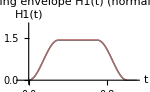

```mathematica
If[exportVideo,ReleaseHold[MoviePlotInner]]
```

```mathematica
frameI=0;
If[exportVideo,
videoDir="video_2000x15_plotpoints";
CreateDirectory[NotebookDirectory[]<>videoDir]
Do[
Print["Rendering frame at t = ",newT];
tM=newT;
frame=ReleaseHold[MoviePlotInner];
Export[ToString@StringForm["````/frame_``.png",NotebookDirectory[],videoDir,StringPadLeft[ToString@frameI,5,"0"]],frame,ImageResolution->200];
frameI++;
,
{newT,0.002,1.0,0.002}
]
];
```

Rendering frame at t = 0.002

Rendering frame at t = 0.004

Rendering frame at t = 0.006

Rendering frame at t = 0.008

Rendering frame at t = 0.01

Rendering frame at t = 0.012

Rendering frame at t = 0.014

Rendering frame at t = 0.016

Rendering frame at t = 0.018

Rendering frame at t = 0.02

Rendering frame at t = 0.022

Rendering frame at t = 0.024

Rendering frame at t = 0.026

Rendering frame at t = 0.028

Rendering frame at t = 0.03

Rendering frame at t = 0.032

Rendering frame at t = 0.034

Rendering frame at t = 0.036

Rendering frame at t = 0.038

Rendering frame at t = 0.04

Rendering frame at t = 0.042

Rendering frame at t = 0.044

Rendering frame at t = 0.046

Rendering frame at t = 0.048

Rendering frame at t = 0.05

Rendering frame at t = 0.052

Rendering frame at t = 0.054

Rendering frame at t = 0.056

Rendering frame at t = 0.058

Rendering frame at t = 0.06

Rendering frame at t = 0.062

Rendering frame at t = 0.064

Rendering frame at t = 0.066

Rendering frame at t = 0.068

Rendering frame at t = 0.07

Rendering frame at t = 0.072

Rendering frame at t = 0.074

Rendering frame at t = 0.076

Rendering frame at t = 0.078

Rendering frame at t = 0.08

Rendering frame at t = 0.082

Rendering frame at t = 0.084

Rendering frame at t = 0.086

Rendering frame at t = 0.088

Rendering frame at t = 0.09

Rendering frame at t = 0.092

Rendering frame at t = 0.094

Rendering frame at t = 0.096

Rendering frame at t = 0.098

Rendering frame at t = 0.1

Rendering frame at t = 0.102

Rendering frame at t = 0.104

Rendering frame at t = 0.106

Rendering frame at t = 0.108

Rendering frame at t = 0.11

Rendering frame at t = 0.112

Rendering frame at t = 0.114

Rendering frame at t = 0.116

Rendering frame at t = 0.118

Rendering frame at t = 0.12

Rendering frame at t = 0.122

Rendering frame at t = 0.124

Rendering frame at t = 0.126

Rendering frame at t = 0.128

Rendering frame at t = 0.13

Rendering frame at t = 0.132

Rendering frame at t = 0.134

Rendering frame at t = 0.136

Rendering frame at t = 0.138

Rendering frame at t = 0.14

Rendering frame at t = 0.142

Rendering frame at t = 0.144

Rendering frame at t = 0.146

Rendering frame at t = 0.148

Rendering frame at t = 0.15

Rendering frame at t = 0.152

Rendering frame at t = 0.154

Rendering frame at t = 0.156

Rendering frame at t = 0.158

Rendering frame at t = 0.16

Rendering frame at t = 0.162

Rendering frame at t = 0.164

Rendering frame at t = 0.166

Rendering frame at t = 0.168

Rendering frame at t = 0.17

Rendering frame at t = 0.172

Rendering frame at t = 0.174

Rendering frame at t = 0.176

Rendering frame at t = 0.178

Rendering frame at t = 0.18

Rendering frame at t = 0.182

Rendering frame at t = 0.184

Rendering frame at t = 0.186

Rendering frame at t = 0.188

Rendering frame at t = 0.19

Rendering frame at t = 0.192

Rendering frame at t = 0.194

Rendering frame at t = 0.196

Rendering frame at t = 0.198

Rendering frame at t = 0.2

Rendering frame at t = 0.202

Rendering frame at t = 0.204

Rendering frame at t = 0.206

Rendering frame at t = 0.208

Rendering frame at t = 0.21

Rendering frame at t = 0.212

Rendering frame at t = 0.214

Rendering frame at t = 0.216

Rendering frame at t = 0.218

Rendering frame at t = 0.22

Rendering frame at t = 0.222

Rendering frame at t = 0.224

Rendering frame at t = 0.226

Rendering frame at t = 0.228

Rendering frame at t = 0.23

Rendering frame at t = 0.232

Rendering frame at t = 0.234

Rendering frame at t = 0.236

Rendering frame at t = 0.238

Rendering frame at t = 0.24

Rendering frame at t = 0.242

Rendering frame at t = 0.244

Rendering frame at t = 0.246

Rendering frame at t = 0.248

Rendering frame at t = 0.25

Rendering frame at t = 0.252

Rendering frame at t = 0.254

Rendering frame at t = 0.256

Rendering frame at t = 0.258

Rendering frame at t = 0.26

Rendering frame at t = 0.262

Rendering frame at t = 0.264

Rendering frame at t = 0.266

Rendering frame at t = 0.268

Rendering frame at t = 0.27

Rendering frame at t = 0.272

Rendering frame at t = 0.274

Rendering frame at t = 0.276

Rendering frame at t = 0.278

Rendering frame at t = 0.28

Rendering frame at t = 0.282

Rendering frame at t = 0.284

Rendering frame at t = 0.286

Rendering frame at t = 0.288

Rendering frame at t = 0.29

Rendering frame at t = 0.292

Rendering frame at t = 0.294

Rendering frame at t = 0.296

Rendering frame at t = 0.298

Rendering frame at t = 0.3

Rendering frame at t = 0.302

Rendering frame at t = 0.304

Rendering frame at t = 0.306

Rendering frame at t = 0.308

Rendering frame at t = 0.31

Rendering frame at t = 0.312

Rendering frame at t = 0.314

Rendering frame at t = 0.316

Rendering frame at t = 0.318

Rendering frame at t = 0.32

Rendering frame at t = 0.322

Rendering frame at t = 0.324

Rendering frame at t = 0.326

Rendering frame at t = 0.328

Rendering frame at t = 0.33

Rendering frame at t = 0.332

Rendering frame at t = 0.334

Rendering frame at t = 0.336

Rendering frame at t = 0.338

Rendering frame at t = 0.34

Rendering frame at t = 0.342

Rendering frame at t = 0.344

Rendering frame at t = 0.346

Rendering frame at t = 0.348

Rendering frame at t = 0.35

Rendering frame at t = 0.352

Rendering frame at t = 0.354

Rendering frame at t = 0.356

Rendering frame at t = 0.358

Rendering frame at t = 0.36

Rendering frame at t = 0.362

Rendering frame at t = 0.364

Rendering frame at t = 0.366

Rendering frame at t = 0.368

Rendering frame at t = 0.37

Rendering frame at t = 0.372

Rendering frame at t = 0.374

Rendering frame at t = 0.376

Rendering frame at t = 0.378

Rendering frame at t = 0.38

Rendering frame at t = 0.382

Rendering frame at t = 0.384

Rendering frame at t = 0.386

Rendering frame at t = 0.388

Rendering frame at t = 0.39

Rendering frame at t = 0.392

Rendering frame at t = 0.394

Rendering frame at t = 0.396

Rendering frame at t = 0.398

Rendering frame at t = 0.4

Rendering frame at t = 0.402

Rendering frame at t = 0.404

Rendering frame at t = 0.406

Rendering frame at t = 0.408

Rendering frame at t = 0.41

Rendering frame at t = 0.412

Rendering frame at t = 0.414

Rendering frame at t = 0.416

Rendering frame at t = 0.418

Rendering frame at t = 0.42

Rendering frame at t = 0.422

Rendering frame at t = 0.424

Rendering frame at t = 0.426

Rendering frame at t = 0.428

Rendering frame at t = 0.43

Rendering frame at t = 0.432

Rendering frame at t = 0.434

Rendering frame at t = 0.436

Rendering frame at t = 0.438

Rendering frame at t = 0.44

Rendering frame at t = 0.442

Rendering frame at t = 0.444

Rendering frame at t = 0.446

Rendering frame at t = 0.448

Rendering frame at t = 0.45

Rendering frame at t = 0.452

Rendering frame at t = 0.454

Rendering frame at t = 0.456

Rendering frame at t = 0.458

Rendering frame at t = 0.46

Rendering frame at t = 0.462

Rendering frame at t = 0.464

Rendering frame at t = 0.466

Rendering frame at t = 0.468

Rendering frame at t = 0.47

Rendering frame at t = 0.472

Rendering frame at t = 0.474

Rendering frame at t = 0.476

Rendering frame at t = 0.478

Rendering frame at t = 0.48

Rendering frame at t = 0.482

Rendering frame at t = 0.484

Rendering frame at t = 0.486

Rendering frame at t = 0.488

Rendering frame at t = 0.49

Rendering frame at t = 0.492

Rendering frame at t = 0.494

Rendering frame at t = 0.496

Rendering frame at t = 0.498

Rendering frame at t = 0.5

Rendering frame at t = 0.502

Rendering frame at t = 0.504

Rendering frame at t = 0.506

Rendering frame at t = 0.508

Rendering frame at t = 0.51

Rendering frame at t = 0.512

Rendering frame at t = 0.514

Rendering frame at t = 0.516

Rendering frame at t = 0.518

Rendering frame at t = 0.52

Rendering frame at t = 0.522

Rendering frame at t = 0.524

Rendering frame at t = 0.526

Rendering frame at t = 0.528

Rendering frame at t = 0.53

Rendering frame at t = 0.532

Rendering frame at t = 0.534

Rendering frame at t = 0.536

Rendering frame at t = 0.538

Rendering frame at t = 0.54

Rendering frame at t = 0.542

Rendering frame at t = 0.544

Rendering frame at t = 0.546

Rendering frame at t = 0.548

Rendering frame at t = 0.55

Rendering frame at t = 0.552

Rendering frame at t = 0.554

Rendering frame at t = 0.556

Rendering frame at t = 0.558

Rendering frame at t = 0.56

Rendering frame at t = 0.562

Rendering frame at t = 0.564

Rendering frame at t = 0.566

Rendering frame at t = 0.568

Rendering frame at t = 0.57

Rendering frame at t = 0.572

Rendering frame at t = 0.574

Rendering frame at t = 0.576

Rendering frame at t = 0.578

Rendering frame at t = 0.58

Rendering frame at t = 0.582

Rendering frame at t = 0.584

Rendering frame at t = 0.586

Rendering frame at t = 0.588

Rendering frame at t = 0.59

Rendering frame at t = 0.592

Rendering frame at t = 0.594

Rendering frame at t = 0.596

Rendering frame at t = 0.598

Rendering frame at t = 0.6

Rendering frame at t = 0.602

Rendering frame at t = 0.604

Rendering frame at t = 0.606

Rendering frame at t = 0.608

Rendering frame at t = 0.61

Rendering frame at t = 0.612

Rendering frame at t = 0.614

Rendering frame at t = 0.616

Rendering frame at t = 0.618

Rendering frame at t = 0.62

Rendering frame at t = 0.622

Rendering frame at t = 0.624

Rendering frame at t = 0.626

Rendering frame at t = 0.628

Rendering frame at t = 0.63

Rendering frame at t = 0.632

Rendering frame at t = 0.634

Rendering frame at t = 0.636

Rendering frame at t = 0.638

Rendering frame at t = 0.64

Rendering frame at t = 0.642

Rendering frame at t = 0.644

Rendering frame at t = 0.646

Rendering frame at t = 0.648

Rendering frame at t = 0.65

Rendering frame at t = 0.652

Rendering frame at t = 0.654

Rendering frame at t = 0.656

Rendering frame at t = 0.658

Rendering frame at t = 0.66

Rendering frame at t = 0.662

Rendering frame at t = 0.664

Rendering frame at t = 0.666

Rendering frame at t = 0.668

Rendering frame at t = 0.67

Rendering frame at t = 0.672

Rendering frame at t = 0.674

Rendering frame at t = 0.676

Rendering frame at t = 0.678

Rendering frame at t = 0.68

Rendering frame at t = 0.682

Rendering frame at t = 0.684

Rendering frame at t = 0.686

Rendering frame at t = 0.688

Rendering frame at t = 0.69

Rendering frame at t = 0.692

Rendering frame at t = 0.694

Rendering frame at t = 0.696

Rendering frame at t = 0.698

Rendering frame at t = 0.7

Rendering frame at t = 0.702

Rendering frame at t = 0.704

Rendering frame at t = 0.706

Rendering frame at t = 0.708

Rendering frame at t = 0.71

Rendering frame at t = 0.712

Rendering frame at t = 0.714

Rendering frame at t = 0.716

Rendering frame at t = 0.718

Rendering frame at t = 0.72

Rendering frame at t = 0.722

Rendering frame at t = 0.724

Rendering frame at t = 0.726

Rendering frame at t = 0.728

Rendering frame at t = 0.73

Rendering frame at t = 0.732

Rendering frame at t = 0.734

Rendering frame at t = 0.736

Rendering frame at t = 0.738

Rendering frame at t = 0.74

Rendering frame at t = 0.742

Rendering frame at t = 0.744

Rendering frame at t = 0.746

Rendering frame at t = 0.748

Rendering frame at t = 0.75

Rendering frame at t = 0.752

Rendering frame at t = 0.754

Rendering frame at t = 0.756

Rendering frame at t = 0.758

Rendering frame at t = 0.76

Rendering frame at t = 0.762

Rendering frame at t = 0.764

Rendering frame at t = 0.766

Rendering frame at t = 0.768

Rendering frame at t = 0.77

Rendering frame at t = 0.772

Rendering frame at t = 0.774

Rendering frame at t = 0.776

Rendering frame at t = 0.778

Rendering frame at t = 0.78

Rendering frame at t = 0.782

Rendering frame at t = 0.784

Rendering frame at t = 0.786

Rendering frame at t = 0.788

Rendering frame at t = 0.79

Rendering frame at t = 0.792

Rendering frame at t = 0.794

Rendering frame at t = 0.796

Rendering frame at t = 0.798

Rendering frame at t = 0.8

Rendering frame at t = 0.802

Rendering frame at t = 0.804

Rendering frame at t = 0.806

Rendering frame at t = 0.808

Rendering frame at t = 0.81

Rendering frame at t = 0.812

Rendering frame at t = 0.814

Rendering frame at t = 0.816

Rendering frame at t = 0.818

Rendering frame at t = 0.82

Rendering frame at t = 0.822

Rendering frame at t = 0.824

Rendering frame at t = 0.826

Rendering frame at t = 0.828

Rendering frame at t = 0.83

Rendering frame at t = 0.832

Rendering frame at t = 0.834

Rendering frame at t = 0.836

Rendering frame at t = 0.838

Rendering frame at t = 0.84

Rendering frame at t = 0.842

Rendering frame at t = 0.844

Rendering frame at t = 0.846

Rendering frame at t = 0.848

Rendering frame at t = 0.85

Rendering frame at t = 0.852

Rendering frame at t = 0.854

Rendering frame at t = 0.856

Rendering frame at t = 0.858

Rendering frame at t = 0.86

Rendering frame at t = 0.862

Rendering frame at t = 0.864

Rendering frame at t = 0.866

Rendering frame at t = 0.868

Rendering frame at t = 0.87

Rendering frame at t = 0.872

Rendering frame at t = 0.874

Rendering frame at t = 0.876

Rendering frame at t = 0.878

Rendering frame at t = 0.88

Rendering frame at t = 0.882

Rendering frame at t = 0.884

Rendering frame at t = 0.886

Rendering frame at t = 0.888

Rendering frame at t = 0.89

Rendering frame at t = 0.892

Rendering frame at t = 0.894

Rendering frame at t = 0.896

Rendering frame at t = 0.898

Rendering frame at t = 0.9

Rendering frame at t = 0.902

Rendering frame at t = 0.904

Rendering frame at t = 0.906

Rendering frame at t = 0.908

Rendering frame at t = 0.91

Rendering frame at t = 0.912

Rendering frame at t = 0.914

Rendering frame at t = 0.916

Rendering frame at t = 0.918

Rendering frame at t = 0.92

Rendering frame at t = 0.922

Rendering frame at t = 0.924

Rendering frame at t = 0.926

Rendering frame at t = 0.928

Rendering frame at t = 0.93

Rendering frame at t = 0.932

Rendering frame at t = 0.934

Rendering frame at t = 0.936

Rendering frame at t = 0.938

Rendering frame at t = 0.94

Rendering frame at t = 0.942

Rendering frame at t = 0.944

Rendering frame at t = 0.946

Rendering frame at t = 0.948

Rendering frame at t = 0.95

Rendering frame at t = 0.952

Rendering frame at t = 0.954

Rendering frame at t = 0.956

Rendering frame at t = 0.958

Rendering frame at t = 0.96

Rendering frame at t = 0.962

Rendering frame at t = 0.964

Rendering frame at t = 0.966

Rendering frame at t = 0.968

Rendering frame at t = 0.97

Rendering frame at t = 0.972

Rendering frame at t = 0.974

Rendering frame at t = 0.976

Rendering frame at t = 0.978

Rendering frame at t = 0.98

Rendering frame at t = 0.982

Rendering frame at t = 0.984

Rendering frame at t = 0.986

Rendering frame at t = 0.988

Rendering frame at t = 0.99

Rendering frame at t = 0.992

Rendering frame at t = 0.994

Rendering frame at t = 0.996

Rendering frame at t = 0.998

Rendering frame at t = 1.

```mathematica
exportVideo=True
```

True

```mathematica
(*Export["3d_cosramp_movie.avi",frames,ImageResolution->300]*)
```